# Notebook for : Decay of solutions of the wave equation in cosmological spacetimes by Rossetti and Vano Vinuales

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
February 15, 2023

```mathematica
(* Currently everything here is wrong... fix this....*)
(* Differentials here are killing you... go back and find how you did this before in other notebook...  *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Paper

```mathematica
Hyperlink["Decay of solutions of the wave equation in cosmological spacetimes by Rossetti and Vano Vinuales",
"https://arxiv.org/abs/1801.08944"]
```

[Decay of solutions of the wave equation in cosmological spacetimes by Rossetti and Vano Vinuales](https://arxiv.org/abs/1801.08944)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 22 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
Clear[dtReplace]
dtReplace = {
 Dt[x]-> dx , 
Dt[y] -> dy , 
Dt[z]-> dz  ,
Dt[𝓇]-> d𝓇 , 
Dt[𝓊]-> d𝓊 , 
Dt[𝓍]-> d𝓍 , 
Dt[τ]-> dτ ,  
Dt[ρ] -> dρ 
} ;
dtReplace // TableForm
```

Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[𝓇]→d𝓇
Dt[𝓊]→d𝓊
Dt[𝓍]→d𝓍
Dt[τ]→dτ
Dt[ρ]→dρ

```mathematica
M/: Dt[M] = 0  ; (* Treat mass as a constant *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 2: FRLW (Not Finished.. Fix Conformal Time )

```mathematica
Clear[eq2]
eq2 = 
a[τ]^2( -dτ^2+ Subscript[dΣ, 3]^2)
```

a[τ]^2 (-dτ^2+dΣ_3^2)

```mathematica
(* Change this.... variables should be primes..... *) 

Clear[conformalTime]
conformalTime = 
τ[t] ==Inactivate[ Integrate[1/a[tprime] , {tprime,0,t}],Integrate] ;
conformalTime // pdConv
```

τ(t)==1/(a(tprime))tprime0t

```mathematica
D[conformalTime,t]
```

τ'[t]==1/a[t]

```mathematica
D[conformalTime,t] /. τ'[t]-> (dτ/dt)
```

dτ/dt==1/a[t]

```mathematica
(* Fix this... *) 

Flatten[Solve[D[conformalTime,t] /. τ'[t]-> (dτ/dt),dt]][[1]]
```

dt→dτ a[t]

```mathematica
Clear[eq3]
eq3 = 
a[τ] == Sinh[((3 w + 1)/2 τ)]^(2/(3w+1))
```

a[τ]==Sinh[1/2 (1+3 w) τ]^(2/(1+3 w))

```mathematica
Clear[spatiallyHyperbolicScale]
spatiallyHyperbolicScale = { 
( eq3 /. Equal-> Rule  )  , 
D[( eq3 /. Equal-> Rule  ),τ] , 
D[( eq3 /. Equal-> Rule  ),{τ,2}]
} // Expand // Simplify ;
spatiallyHyperbolicScale // TableForm // pdConv
```

a(τ)→sinh^(2/(3 w+1))(1/2 τ (3 w+1))
(∂a(τ))/(∂τ)→sinh^(2/(3 w+1)-1)(1/2 τ (3 w+1)) cosh(1/2 τ (3 w+1))
(∂^2 a(τ))/(∂τ^2)→1/2 sinh^(-(6 w)/(3 w+1))(1/2 τ (3 w+1)) (cosh(τ+3 τ w)-3 w)

```mathematica
Clear[pressure]
pressure = 
p == 2/(3(1+w))
```

p==2/(3 (1+w))

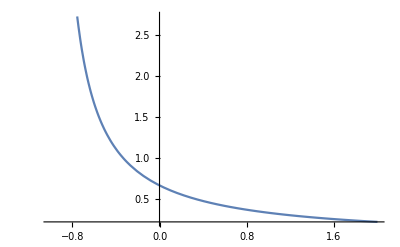

```mathematica
Plot[pressure [[2]] , {w,-1,2}]
```

```mathematica
Clear[scaleFactor]
scaleFactor = 
a[t] == t^p
```

a[t]==t^p

```mathematica
Clear[scaleFactorDerivatives]
scaleFactorDerivatives = { 
scaleFactor  , 
D[scaleFactor,t] , 
D[scaleFactor,{t,2}]
} /. Equal-> Rule ;
scaleFactorDerivatives // TableForm
```

a[t]→t^p
a'[t]→p t^(-1+p)
a''[t]→(-1+p) p t^(-2+p)

```mathematica
Clear[eq4]
eq4 = 
Subscript[dΣ, 3]^2 == dr^2+ Sinh[r]^2 ( dθ^2+ Sin[θ]^2 dϕ^2)
```

dΣ_3^2==dr^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[r]^2

```mathematica
eq2 /. ( eq4 /. Equal-> Rule )
```

a[τ]^2 (dr^2-dτ^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[r]^2)

```mathematica
Clear[metric2]
metric2 = 
lineToMetric[( eq2 /. ( eq4 /. Equal-> Rule )),{dτ,dr,dθ,dϕ} ] ;
metric2 // MatrixForm // pdConv
```

(-(a(τ))^2 | 0 | 0 | 0
0 | (a(τ))^2 | 0 | 0
0 | 0 | (a(τ))^2 sinh^2(r) | 0
0 | 0 | 0 | (a(τ))^2 sin^2(θ) sinh^2(r))

## Calculation of Tensors Associated With Metric 2: FRLW

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 4.88 for all tensors *)
input[ "metric2", metric2, "FRLW","g^frlw",{t,r,θ,ϕ}, "Greek"] // Timing
```

{1.8575,Null}

```mathematica
tensorList[[1]]
TensorName[tensorList[[1]]]
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^frlw)_αβ^

FRLW

(-(a(τ))^2 | 0 | 0 | 0
0 | (a(τ))^2 | 0 | 0
0 | 0 | (a(τ))^2 sinh^2(r) | 0
0 | 0 | 0 | (a(τ))^2 sin^2(θ) sinh^2(r))

```mathematica
tensorList[[2]]
TensorName[tensorList[[2]]]
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolFRLW

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
sinh(r) (-cosh(r))
0) | (0
0
0
sin^2(θ) sinh(r) (-cosh(r)))
(0
0
0
0) | (0
0
coth(r)
0) | (0
coth(r)
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
coth(r)) | (0
0
0
cot(θ)) | (0
coth(r)
cot(θ)
0))

```mathematica
tensorList[[3]]
TensorName[tensorList[[3]]]
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(a(τ))^2 sinh^2(r) | 0
0 | (a(τ))^2 sinh^2(r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(a(τ))^2 sin^2(θ) sinh^2(r)
0 | 0 | 0 | 0
0 | (a(τ))^2 sin^2(θ) sinh^2(r) | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (a(τ))^2 sinh^2(r) | 0
0 | -(a(τ))^2 sinh^2(r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(a(τ))^2 sin^2(θ) sinh^4(r)
0 | 0 | (a(τ))^2 sin^2(θ) sinh^4(r) | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (a(τ))^2 sin^2(θ) sinh^2(r)
0 | 0 | 0 | 0
0 | -(a(τ))^2 sin^2(θ) sinh^2(r) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | (a(τ))^2 sin^2(θ) sinh^4(r)
0 | 0 | -(a(τ))^2 sin^2(θ) sinh^4(r) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]]
TensorName[tensorList[[4]]]
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorFRLW

(0 | 0 | 0 | 0
0 | -2 | 0 | 0
0 | 0 | -2 sinh^2(r) | 0
0 | 0 | 0 | -2 sin^2(θ) sinh^2(r))

```mathematica
tensorList[[5]]
TensorName[tensorList[[5]]]
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarFRLW

-6/(a(τ))^2

```mathematica
tensorList[[6]]
TensorName[tensorList[[6]]]
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarFRLW

12/(a(τ))^4

```mathematica
tensorList[[7]]
TensorName[tensorList[[7]]]
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorFRLW

(-3 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | sinh^2(r) | 0
0 | 0 | 0 | sin^2(θ) sinh^2(r))

```mathematica
tensorList[[8]]
TensorName[tensorList[[8]]]
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorFRLW

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]]
TensorName[tensorList[[9]]]
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorFRLW

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

## Wave Equation (Our Derivation - Currently Wrong - Fix This )

```mathematica
Clear[inverseMetric]
inverseMetric = 
Inverse[metric2] ;
inverseMetric // MatrixForm // pdConv
```

(-1/(a(τ))^2 | 0 | 0 | 0
0 | 1/(a(τ))^2 | 0 | 0
0 | 0 | (csch^2(r))/(a(τ))^2 | 0
0 | 0 | 0 | (csc^2(θ) csch^2(r))/(a(τ))^2)

```mathematica
Clear[rootMinusG]
rootMinusG = 
PowerExpand[Sqrt[(-1)*Det[metric2]]]
```

a[τ]^4 Sin[θ] Sinh[r]^2

```mathematica
Clear[variables]
variables = 
{t,r,θ,ϕ}
```

{t,r,θ,ϕ}

```mathematica
Clear[waveEquation]
waveEquation = 
(1/rootMinusG)Sum[ D[( rootMinusG * inverseMetric[[μ,ν]] D[ϕ[τ,r,θ,ϕ],variables[[ν]]] )  , variables[[μ]] ],{μ,1,4},{ν,1,4}]  // Expand   ;
waveEquation  // pdConv
```

((∂^2 ϕ(τ,r,θ,ϕ))/(∂r^2))/(a(τ))^2+(csch^2(r) (∂^2 ϕ(τ,r,θ,ϕ))/(∂θ^2))/(a(τ))^2+(csc^2(θ) csch^2(r) (∂^2 ϕ(τ,r,θ,ϕ))/(∂ϕ^2))/(a(τ))^2+(2 coth(r) (∂ϕ(τ,r,θ,ϕ))/(∂r))/(a(τ))^2+(cot(θ) csch^2(r) (∂ϕ(τ,r,θ,ϕ))/(∂θ))/(a(τ))^2

```mathematica
Flatten[Solve[ waveEquation  == 0 , Derivative[2,0,0,0][ϕ][t,r,θ,ϕ]]][[1]] /. Rule-> Equal // pdConv
```

(∂^2 ϕ(t,r,θ,ϕ))/(∂t^2)==(∂^2 ϕ(t,r,θ,ϕ))/(∂r^2)+csch^2(r) (∂^2 ϕ(t,r,θ,ϕ))/(∂θ^2)+csc^2(θ) csch^2(r) (∂^2 ϕ(t,r,θ,ϕ))/(∂ϕ^2)+2 coth(r) (∂ϕ(t,r,θ,ϕ))/(∂r)+cot(θ) csch^2(r) (∂ϕ(t,r,θ,ϕ))/(∂θ)

## Wave Equation (Taken Directly From Documentation for GRTensors - Examples - Wave Equations )

```mathematica
phi=ToTensor[{"PhiScalar","ϕ"},tensorList[[1]],ϕ[t,r]Ylm[θ,ϕ]]
```

ϕ

```mathematica
Timing[waveScalar1=CovariantD[phi,-α,α]]
```

{0.019077,(g^frlw)_^αβ (-Γ_αβ^γ (∂ϕ)_γ^+(∂(∂ϕ))_βα^)}

```mathematica
Timing[boxPhi1=MergeTensors[waveScalar1,ActWith->(Collect[#,{_[θ,ϕ],_[t,r]},Simplify]&)]]
```

{0.1064,(((-1)·((g^frlw·Γ)·(∂ϕ)))+(g^frlw·(∂(∂ϕ))))}

```mathematica
boxPhi1//TensorValues
```

(Csc[θ]^2 Csch[r]^2 ϕ[t,r] Ylm^(0,2)[θ,ϕ])/a[τ]^2+(Cot[θ] Csch[r]^2 ϕ[t,r] Ylm^(1,0)[θ,ϕ])/a[τ]^2+(Csch[r]^2 ϕ[t,r] Ylm^(2,0)[θ,ϕ])/a[τ]^2+Ylm[θ,ϕ] ((2 Coth[r] ϕ^(0,1)[t,r])/a[τ]^2+(ϕ^(0,2)[t,r])/a[τ]^2-(ϕ^(2,0)[t,r])/a[τ]^2)

```mathematica
Clear[d2thYRule,dphYRule]
d2thYRule=Derivative[a_/;a≥2,b_][Ylm][θ,ϕ]:>D[(m^2/Sin[θ]^2-l (1+l))Ylm[θ,ϕ]-Cos[θ]/Sin[θ] D[Ylm[θ,ϕ],θ],{θ,a-2},{ϕ,b}];
dphYRule=Derivative[a_,b_][Ylm][θ,ϕ]:>D[(I m)^b Ylm[θ,ϕ],{θ,a}];
removeYlmDerivs[expr_]:=expr//.{d2thYRule,dphYRule};
collectAndSimp[expr_]:=Collect[removeYlmDerivs@expr,{_[θ,ϕ],_[t,r]},Simplify]
```

```mathematica
Timing[boxPhi2=ActOnTensorValues[collectAndSimp,boxPhi1]]
```

{0.013069,(((-1)·((g^frlw·Γ)·(∂ϕ)))+(g^frlw·(∂(∂ϕ))))}

```mathematica
boxPhi2//TensorValues // pdConv
```

Ylm(θ,ϕ) (-(l (l+1) csch^2(r) ϕ(t,r))/(a(τ))^2+((∂^2 ϕ(t,r))/(∂r^2))/(a(τ))^2-((∂^2 ϕ(t,r))/(∂t^2))/(a(τ))^2+(2 coth(r) (∂ϕ(t,r))/(∂r))/(a(τ))^2)

```mathematica
Flatten[Solve[ TensorValues[boxPhi2][[2]]==0 ,Derivative[2,0][ϕ][t,r]]][[1]] /. Rule-> Equal  // pdConv
```

(∂^2 ϕ(t,r))/(∂t^2)==-l^2 csch^2(r) ϕ(t,r)-l csch^2(r) ϕ(t,r)+(∂^2 ϕ(t,r))/(∂r^2)+2 coth(r) (∂ϕ(t,r))/(∂r)

## Flat Case Metric

```mathematica
Clear[flatCase]
flatCase = 
-dt^2+ t^(2p) ( dx1^2+ dx2^2+ dx3^2)
```

-dt^2+(dx1^2+dx2^2+dx3^2) t^(2 p)

```mathematica
Clear[flatCaseMetric]
flatCaseMetric = 
lineToMetric[flatCase,{dt,dx1,dx2,dx3}] ;
flatCaseMetric // MatrixForm // pdConv
```

(-1 | 0 | 0 | 0
0 | t^(2 p) | 0 | 0
0 | 0 | t^(2 p) | 0
0 | 0 | 0 | t^(2 p))

## Calculation of Tensors For Flat Case Metric

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input2] 
input2[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList2];
tensorList2 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList2[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList2[[2]]  = 
ChristoffelSymbol[ tensorList2[[1]] , ActWith-> Simplify] ;
tensorList2[[3]] = 
RiemannTensor[ tensorList2[[1]] , ActWithNested-> Simplify ];
tensorList2[[4]] = 
RicciTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;
tensorList2[[5]] = 
RicciScalar[ tensorList2[[1]] , ActWith-> Simplify ] ;
 tensorList2[[6]] = 
KretschmannScalar[ tensorList2[[1]] , ActWith-> Simplify] ; 
tensorList2[[7]] = 
EinsteinTensor[ tensorList2[[1]] , ActWith-> Simplify] ;  
tensorList2[[8]] = 
WeylTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;
 tensorList2[[9]] = 
CottonTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;  
];
```

```mathematica
(* Last timing took 1.55 for all tensors *)
input2[ "flatCase",flatCaseMetric, "flatCase","g^flat",{t,r,θ,ϕ}, "Greek"] // Timing
```

{1.55334,Null}

```mathematica
tensorList2
```

{(g^flat)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList2[[1]] 
TensorName[tensorList2[[1]]] 
TensorValues[tensorList2[[1]]] // MatrixForm // pdConv
```

(g^flat)_αβ^

flatCase

(-1 | 0 | 0 | 0
0 | t^(2 p) | 0 | 0
0 | 0 | t^(2 p) | 0
0 | 0 | 0 | t^(2 p))

```mathematica
tensorList2[[2]] 
TensorName[tensorList2[[2]]] 
TensorValues[tensorList2[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolflatCase

((0
0
0
0) | (0
p t^(2 p-1)
0
0) | (0
0
p t^(2 p-1)
0) | (0
0
0
p t^(2 p-1))
(0
p/t
0
0) | (p/t
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
p/t
0) | (0
0
0
0) | (p/t
0
0
0) | (0
0
0
0)
(0
0
0
p/t) | (0
0
0
0) | (0
0
0
0) | (p/t
0
0
0))

```mathematica
tensorList2[[3]] 
TensorName[tensorList2[[3]]] 
TensorValues[tensorList2[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorflatCase

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -((p-1) p t^(2 p-2)) | 0 | 0
(p-1) p t^(2 p-2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | -((p-1) p t^(2 p-2)) | 0
0 | 0 | 0 | 0
(p-1) p t^(2 p-2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -((p-1) p t^(2 p-2))
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(p-1) p t^(2 p-2) | 0 | 0 | 0)
(0 | (p-1) p t^(2 p-2) | 0 | 0
-((p-1) p t^(2 p-2)) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | p^2 t^(4 p-2) | 0
0 | -p^2 t^(4 p-2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | p^2 t^(4 p-2)
0 | 0 | 0 | 0
0 | -p^2 t^(4 p-2) | 0 | 0)
(0 | 0 | (p-1) p t^(2 p-2) | 0
0 | 0 | 0 | 0
-((p-1) p t^(2 p-2)) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -p^2 t^(4 p-2) | 0
0 | p^2 t^(4 p-2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | p^2 t^(4 p-2)
0 | 0 | -p^2 t^(4 p-2) | 0)
(0 | 0 | 0 | (p-1) p t^(2 p-2)
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-((p-1) p t^(2 p-2)) | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -p^2 t^(4 p-2)
0 | 0 | 0 | 0
0 | p^2 t^(4 p-2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -p^2 t^(4 p-2)
0 | 0 | p^2 t^(4 p-2) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList2[[4]] 
TensorName[tensorList2[[4]]] 
TensorValues[tensorList2[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorflatCase

(-(3 (p-1) p)/t^2 | 0 | 0 | 0
0 | p (3 p-1) t^(2 p-2) | 0 | 0
0 | 0 | p (3 p-1) t^(2 p-2) | 0
0 | 0 | 0 | p (3 p-1) t^(2 p-2))

```mathematica
tensorList2[[5]] 
TensorName[tensorList2[[5]]] 
TensorValues[tensorList2[[5]]] // MatrixForm // pdConv
```

R

RicciScalarflatCase

(6 p (2 p-1))/t^2

```mathematica
tensorList2[[6]] 
TensorName[tensorList2[[6]]] 
TensorValues[tensorList2[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarflatCase

(12 p^2 (2 p^2-2 p+1))/t^4

```mathematica
tensorList2[[7]] 
TensorName[tensorList2[[7]]] 
TensorValues[tensorList2[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorflatCase

((3 p^2)/t^2 | 0 | 0 | 0
0 | -p (3 p-2) t^(2 p-2) | 0 | 0
0 | 0 | -p (3 p-2) t^(2 p-2) | 0
0 | 0 | 0 | -p (3 p-2) t^(2 p-2))

```mathematica
tensorList2[[8]] 
TensorName[tensorList2[[8]]] 
TensorValues[tensorList2[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorflatCase

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList2[[9]] 
TensorName[tensorList2[[9]]] 
TensorValues[tensorList2[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorflatCase

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

## Hyperbolic Metric

```mathematica
Clear[hyperbolicCase]
hyperbolicCase = 
-dt^2+ a[t]^2 (dr^2+ Sinh[r]^2(dθ^2+ Sin[θ]^2 dϕ^2))
```

-dt^2+a[t]^2 (dr^2+(dθ^2+dϕ^2 Sin[θ]^2) Sinh[r]^2)

```mathematica
Clear[hyperbolicCaseMetric]
hyperbolicCaseMetric = 
lineToMetric[hyperbolicCase,{dt,dr,dθ,dϕ}]  ;
hyperbolicCaseMetric// MatrixForm // pdConv
```

(-1 | 0 | 0 | 0
0 | (a(t))^2 | 0 | 0
0 | 0 | (a(t))^2 sinh^2(r) | 0
0 | 0 | 0 | (a(t))^2 sin^2(θ) sinh^2(r))

## Calculation of Tensors For Hyperbolic Metric

```mathematica
Clear[input3] 
input3[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList3];
tensorList3 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList3[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList3[[2]]  = 
ChristoffelSymbol[ tensorList3[[1]] , ActWith-> Simplify] ;
tensorList3[[3]] = 
RiemannTensor[ tensorList3[[1]]    , ActWithNested-> Simplify   ];
tensorList3[[4]] = 
RicciTensor[ tensorList3[[1]]   , ActWith-> Simplify   ] ;
tensorList3[[5]] = 
RicciScalar[ tensorList3[[1]]    , ActWith-> Simplify   ] ;
 tensorList3[[6]] = 
KretschmannScalar[ tensorList3[[1]] , ActWith-> Simplify] ; 
tensorList3[[7]] = 
EinsteinTensor[ tensorList3[[1]]    , ActWith-> Simplify  ] ; 
 tensorList3[[8]] = 
WeylTensor[ tensorList3[[1]] , ActWith-> Simplify ] ;
 tensorList3[[9]] = 
CottonTensor[ tensorList3[[1]] , ActWith-> Simplify ] ; 
];
```

```mathematica
(* Last timing took 18.92 for all tensors *) 
input3[ "hyperbolicCaseMetric", hyperbolicCaseMetric, "Hyperbolic","g^hyperbolic",{t,r,θ,ϕ},"Greek"] // Timing
```

{2.91067,Null}

```mathematica
tensorList3
```

{(g^hyperbolic)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList3[[1]]
TensorName[tensorList3[[1]]]
TensorValues[tensorList3[[1]]] // MatrixForm// pdConv
```

(g^hyperbolic)_αβ^

Hyperbolic

(-1 | 0 | 0 | 0
0 | (a(t))^2 | 0 | 0
0 | 0 | (a(t))^2 sinh^2(r) | 0
0 | 0 | 0 | (a(t))^2 sin^2(θ) sinh^2(r))

```mathematica
tensorList3[[2]]
TensorName[tensorList3[[2]]]
TensorValues[tensorList3[[2]]]// MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolHyperbolic

((0
0
0
0) | (0
a(t) (∂a(t))/(∂t)
0
0) | (0
0
a(t) sinh^2(r) (∂a(t))/(∂t)
0) | (0
0
0
a(t) sin^2(θ) sinh^2(r) (∂a(t))/(∂t))
(0
((∂a(t))/(∂t))/(a(t))
0
0) | (((∂a(t))/(∂t))/(a(t))
0
0
0) | (0
0
sinh(r) (-cosh(r))
0) | (0
0
0
sin^2(θ) sinh(r) (-cosh(r)))
(0
0
((∂a(t))/(∂t))/(a(t))
0) | (0
0
coth(r)
0) | (((∂a(t))/(∂t))/(a(t))
coth(r)
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
((∂a(t))/(∂t))/(a(t))) | (0
0
0
coth(r)) | (0
0
0
cot(θ)) | (((∂a(t))/(∂t))/(a(t))
coth(r)
cot(θ)
0))

```mathematica
tensorList3[[1]]
TensorName[tensorList3[[1]]]
TensorValues[tensorList3[[1]]] // MatrixForm// pdConv
```

(g^hyperbolic)_αβ^

Hyperbolic

(-1 | 0 | 0 | 0
0 | (a(t))^2 | 0 | 0
0 | 0 | (a(t))^2 sinh^2(r) | 0
0 | 0 | 0 | (a(t))^2 sin^2(θ) sinh^2(r))

```mathematica
tensorList3[[4]]
TensorName[tensorList3[[4]]]
TensorValues[tensorList3[[4]]] // MatrixForm// pdConv
```

R_βγ^

RicciTensorHyperbolic

(-(3 (∂^2 a(t))/(∂t^2))/(a(t)) | 0 | 0 | 0
0 | a(t) (∂^2 a(t))/(∂t^2)+2 ((∂a(t))/(∂t))^2-2 | 0 | 0
0 | 0 | sinh^2(r) (a(t) (∂^2 a(t))/(∂t^2)+2 ((∂a(t))/(∂t))^2-2) | 0
0 | 0 | 0 | sin^2(θ) sinh^2(r) (a(t) (∂^2 a(t))/(∂t^2)+2 ((∂a(t))/(∂t))^2-2))

```mathematica
tensorList3[[5]]
TensorName[tensorList3[[5]]]
 TensorValues[tensorList3[[5]]] // MatrixForm// pdConv
```

R

RicciScalarHyperbolic

(6 (a(t) (∂^2 a(t))/(∂t^2)+((∂a(t))/(∂t))^2-1))/(a(t))^2

```mathematica
tensorList3[[6]]
TensorName[tensorList3[[6]]]
TensorValues[tensorList3[[6]]] // MatrixForm// pdConv
```

K

KretschmannScalarHyperbolic

(12 ((a(t))^2 ((∂^2 a(t))/(∂t^2))^2+((∂a(t))/(∂t))^4-2 ((∂a(t))/(∂t))^2+1))/(a(t))^4

```mathematica
tensorList3[[7]]
TensorName[tensorList3[[7]]]
TensorValues[tensorList3[[7]]] // MatrixForm// pdConv
```

G_αβ^

EinsteinTensorHyperbolic

((3 (((∂a(t))/(∂t))^2-1))/(a(t))^2 | 0 | 0 | 0
0 | -2 a(t) (∂^2 a(t))/(∂t^2)-((∂a(t))/(∂t))^2+1 | 0 | 0
0 | 0 | -(sinh^2(r) (2 a(t) (∂^2 a(t))/(∂t^2)+((∂a(t))/(∂t))^2-1)) | 0
0 | 0 | 0 | -(sin^2(θ) sinh^2(r) (2 a(t) (∂^2 a(t))/(∂t^2)+((∂a(t))/(∂t))^2-1)))

```mathematica
tensorList3[[8]]
TensorName[tensorList3[[8]]]
TensorValues[tensorList3[[8]]] // MatrixForm// pdConv
```

C_αβγδ^

WeylTensorHyperbolic

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList3[[9]]
TensorName[tensorList3[[9]]]
TensorValues[tensorList3[[9]]] // MatrixForm// pdConv
```

C_αβγ^

CottonTensorHyperbolic

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))